```mathematica
ins[lay_, dat_, curs_, level_]:=Module[{newCurs=curs, res={}, i, worked=0},(
For[i=1,i<= Length@lay,i++,(n=lay[[i]];worked++;
If[n==0,
(in=ins[lay[[i+1;;-1]], dat, newCurs,level+1];{sub,wrk, ncs}=in;res=Join[res,{sub}];i+=wrk;worked+=wrk;newCurs=ncs;),
 If[n==-1,
(Return[{res, worked, newCurs}];),
(newCurs=newCurs+n;res=Join[res,dat[[newCurs-n;;newCurs-1]]];)]];)];
Return[{res, worked, newCurs}]
)]
```

```mathematica
Clear[fun]
fun[te_, strt_, side_]:=(p={te[[2]],strt};dir={0,side};
If[te[[1]]==1,(p=Reverse[p];dir=Reverse[dir])];Sow[{p,p+999*dir},"segs"];
If[Depth@te[[3]]>2,(perp1=te[[3,1]]≠te[[1]];fun[te[[3]],If[perp1,te[[2]],strt],If[perp1,-1,side]]), Sow[#, "points"]&/@te[[3]]];
If[Depth@te[[4]]>2,(perp2=te[[4,1]]≠te[[1]];fun[te[[4]],If[perp2,te[[2]],strt],If[perp2,+1,side]]), Sow[#, "points"]&/@te[[4]]];)
messageHandler=If[Last[#],Abort[]]&;
Internal`AddHandler["Message",messageHandler]
```

```mathematica
LoadTree[filename_]:=Module[{file,num,data,layout,kdGrid,base,stopper,cand,segs,points},
file = OpenRead[filename, BinaryFormat->True];
num=First@BinaryReadList[file, "Integer32",1];
data=BinaryReadList[file, "Real64", num];
layout=BinaryReadList[file, "Integer32"];
Close[file];

kdGrid=ins[layout, data, 1,0][[1,1]];
{segs, points}=Reap[fun[kdGrid,0,1], {"segs","points"}][[2,All,1]];
points=Partition[points,2];
For[i=1,i<=Length@segs, i++,
(
axisi = If[segs[[i,1,1]]==segs[[i,2,1]],0,1];
axcmpl=1-axisi;
{base,stopper}=segs[[i,{1,2},axcmpl+1]];
sj=0;
For[j=1,j<i, j++,
(
axisj = If[segs[[j,1,1]]==segs[[j,2,1]],0,1];
If[axisi≠axisj&&Between[segs[[i,1,axisi+1]],segs[[j,{1,2},axisi+1]]],(cand=segs[[j,1,axisj+1]];If[base>cand>stopper || base<cand<stopper,(stopper = cand; sj=j;)])]
)];
segs[[i,2,axcmpl+1]]=stopper;
)];

Return@{segs, points}]
```

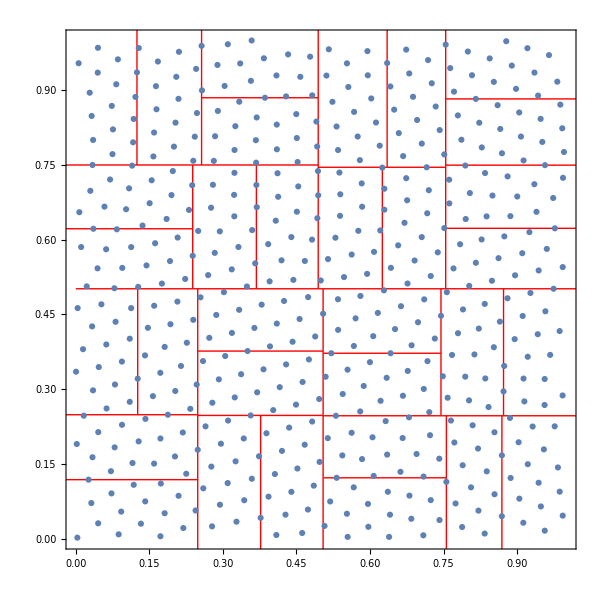

```mathematica
{segs, points}=LoadTree[NotebookDirectory[]<>"out/x64-Release/kdtree.binary"];
kdtreeplot=ListPlot[points,PlotRange->{{0,1},{0,1}},Frame->True,PlotRangeClipping->True,Prolog->{Red,Line[segs]},PlotRangePadding->0,PlotRange->All,AspectRatio->1,ImageSize->600]
```